#### Задание 22

а) Составить сетевой план комплекса работ. Упорядочить структурную таблицу. 
б) Построить сетевой граф работа-вершина и вершина-событие. 
в) Построить временной сетевой граф: диаграмму Ганта и линейчатый граф. 
г) Построить временной сетевой граф на основе графа вершина-событие и граф с указанием резервов времени. 
д) Найти для всех вариантов временного графа: резерв времени события, ранний срок свершения события, поздний срок свершения события, резерв времени работы, свободный резерв времени работы. 
е) Построить математическую модель получения сетевого плана и реализовать ее.

Структурная таблица

```mathematica
tasks=Sort[{{1,13,{}},{2,5,{}},{3,25,{}},{4,20,{2}},{5,7,{1,6}},{6,3,{7}},{7,4,{2}},{8,6,{3,4,9}},{9,3,{12,13}},{10,10,{7}},{11,22,{7}},{12,14,{5,10}},{13,2,{3,4,14}},{14,12,{5,10}},{15,23,{12,13}}},First];
```

```mathematica
TableForm[tasks,TableDepth->2,TableHeadings->{None,{"№", "duration", "follows №"}}]
```

№ | duration | follows №
1 | 13 | {}
2 | 5 | {}
3 | 25 | {}
4 | 20 | {2}
5 | 7 | {1,6}
6 | 3 | {7}
7 | 4 | {2}
8 | 6 | {3,4,9}
9 | 3 | {12,13}
10 | 10 | {7}
11 | 22 | {7}
12 | 14 | {5,10}
13 | 2 | {3,4,14}
14 | 12 | {5,10}
15 | 23 | {12,13}

```mathematica
schedule=Append[#,If[#[[3]]==={},1,Undefined]]&/@tasks;
```

```mathematica
TableForm[schedule,TableDepth->2,TableHeadings->{None,{"№", "duration", "follows №","level"}}]
```

№ | duration | follows № | level
1 | 13 | {} | 1
2 | 5 | {} | 1
3 | 25 | {} | 1
4 | 20 | {2} | Undefined
5 | 7 | {1,6} | Undefined
6 | 3 | {7} | Undefined
7 | 4 | {2} | Undefined
8 | 6 | {3,4,9} | Undefined
9 | 3 | {12,13} | Undefined
10 | 10 | {7} | Undefined
11 | 22 | {7} | Undefined
12 | 14 | {5,10} | Undefined
13 | 2 | {3,4,14} | Undefined
14 | 12 | {5,10} | Undefined
15 | 23 | {12,13} | Undefined

```mathematica
ClearAll[nestWBS];
nestWBS[wbs_List]:=Module[
{},
Table[
ReplacePart[
wbs⟦i⟧,
4->If[
wbs⟦i,4⟧===Undefined,
Max[
Select[
wbs,
MemberQ[wbs⟦i,3⟧,#[[1]]]&
]⟦All,4⟧]+1,
wbs⟦i,4⟧]],
{i,Length@schedule}]
]
```

```mathematica
wbs=NestWhile[nestWBS,schedule,MemberQ[#,Undefined,2]&];
```

```mathematica
TableForm[wbs,TableDepth->2,TableHeadings->{None,{"№", "duration", "follows №","level"}}]
```

№ | duration | follows № | level
1 | 13 | {} | 1
2 | 5 | {} | 1
3 | 25 | {} | 1
4 | 20 | {2} | 2
5 | 7 | {1,6} | 4
6 | 3 | {7} | 3
7 | 4 | {2} | 2
8 | 6 | {3,4,9} | 8
9 | 3 | {12,13} | 7
10 | 10 | {7} | 3
11 | 22 | {7} | 3
12 | 14 | {5,10} | 5
13 | 2 | {3,4,14} | 6
14 | 12 | {5,10} | 5
15 | 23 | {12,13} | 7

```mathematica
sortedWBS=SortBy[wbs,Last];
```

```mathematica
TableForm[sortedWBS,TableDepth->2,TableHeadings->{None,{"№", "duration", "follows №","level"}}]
```

№ | duration | follows № | level
1 | 13 | {} | 1
2 | 5 | {} | 1
3 | 25 | {} | 1
4 | 20 | {2} | 2
7 | 4 | {2} | 2
6 | 3 | {7} | 3
10 | 10 | {7} | 3
11 | 22 | {7} | 3
5 | 7 | {1,6} | 4
12 | 14 | {5,10} | 5
14 | 12 | {5,10} | 5
13 | 2 | {3,4,14} | 6
9 | 3 | {12,13} | 7
15 | 23 | {12,13} | 7
8 | 6 | {3,4,9} | 8

```mathematica
rules=Thread[sortedWBS⟦All,1⟧->Range[Length@sortedWBS]]
```

{1→1,2→2,3→3,4→4,7→5,6→6,10→7,11→8,5→9,12→10,14→11,13→12,9→13,15→14,8→15}

```mathematica
data=Replace[ReplaceAt[sortedWBS,rules,{All,1}],rules,{3}];
```

```mathematica
TableForm[data,TableDepth->2,TableHeadings->{None,{"№", "duration", "follows №","level"}}]
```

№ | duration | follows № | level
1 | 13 | {} | 1
2 | 5 | {} | 1
3 | 25 | {} | 1
4 | 20 | {2} | 2
5 | 4 | {2} | 2
6 | 3 | {5} | 3
7 | 10 | {5} | 3
8 | 22 | {5} | 3
9 | 7 | {1,6} | 4
10 | 14 | {9,7} | 5
11 | 12 | {9,7} | 5
12 | 2 | {3,4,11} | 6
13 | 3 | {10,12} | 7
14 | 23 | {10,12} | 7
15 | 6 | {3,4,13} | 8

```mathematica
dependA=Association[Thread[data⟦All,1⟧->data⟦All,3⟧]];
```

```mathematica
durationA=Association[Thread[data⟦All,1⟧->data⟦All,2⟧]];
```

Ориентированный граф по исходной таблице (до ранжирования)

```mathematica
first0=Select[schedule,#[[3]]==={}&]⟦All,1⟧;
```

```mathematica
last0=DeleteElements[schedule⟦All,1⟧,DeleteDuplicates@Flatten@schedule⟦All,3⟧];
```

```mathematica
edges0=Join[
Flatten[Thread/@Thread[DirectedEdge[schedule⟦All,3⟧,schedule⟦All,1⟧]]],
Thread[DirectedEdge["start",first0]],
Thread[DirectedEdge[last0,"end"]]
];
```

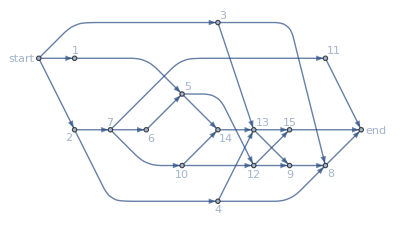

```mathematica
LayeredGraphPlot[
edges0,
Left,
VertexLabels->"Name"]
```

Ориентированный граф по упорядоченной структурной таблице

```mathematica
first=Select[data,#[[3]]==={}&]⟦All,1⟧;
```

```mathematica
last=DeleteElements[data⟦All,1⟧,DeleteDuplicates@Flatten@data⟦All,3⟧];
```

```mathematica
edges=Join[
Flatten[Thread/@Thread[DirectedEdge[data⟦All,3⟧,data⟦All,1⟧]]],
Thread[DirectedEdge["start",first]],
Thread[DirectedEdge[last,"end"]]
];
```

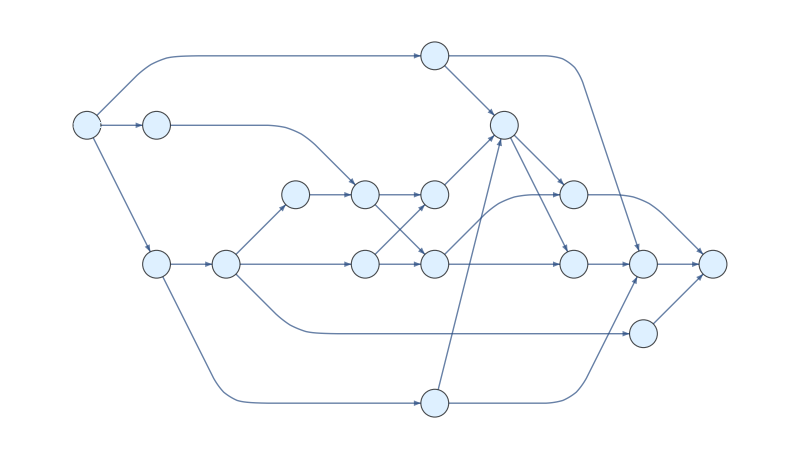

```mathematica
Graph[
edges,
VertexSize->0.4,
VertexLabels->Placed[Automatic,Center],
VertexLabelStyle->Bold,
VertexStyle->LightBlue,
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left},
ImageSize->800]
```

```mathematica
vertexCoords={
"start"->{0.0,0.0},
1->{1,1},
2->{1,0},
3->{1,-2},
4->{2,-1},
5->{2,0},
6->{3,0},
7->{3,1},
8->{3,-2.5},
9->{4,0},
10->{5,1},
11->{5,0},
12->{6,-0.5},
13->{7,0},
14->{7,1},
15->{8,-1},
"end"->{9.5,-1}
};
```

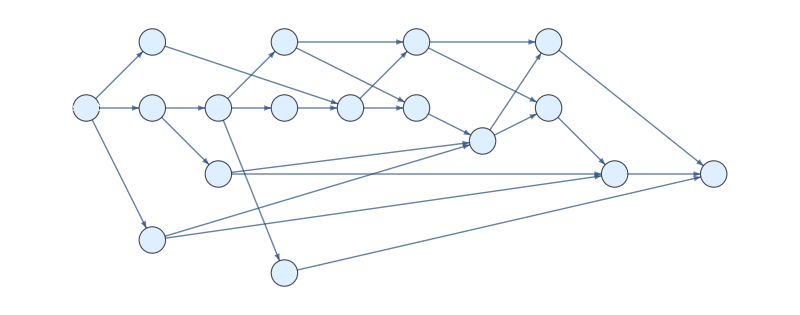

```mathematica
Graph[
edges,
VertexSize->0.4,
VertexLabels->Placed[Automatic,Center],
VertexLabelStyle->Bold,
VertexStyle->LightBlue,
VertexCoordinates->vertexCoords,
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left},
ImageSize->800]
```

Сетевой граф “работа-вершина”

Диаграмма Ганта

```mathematica
ClearAll[getTimes]
getTimes[wbs_List]:=Module[
{table=Append[#,0]&/@wbs},
Do[
table=ReplacePart[
table,
{i,-1}->table⟦i,2⟧+Max[
Max[
Select[
table,
MemberQ[table⟦i,3⟧,#[[1]]]&
]⟦All,-1⟧],
0]
],
{i,Length@table}];
Join[table,Transpose@{table⟦All,-1⟧-table⟦All,2⟧},2]⟦All,{1,4,3,2,6,5}⟧
]
```

```mathematica
earlyTimesdata=getTimes[data];
```

```mathematica
TableForm[earlyTimesdata,TableDepth->2,TableHeadings->{None,{"№", "level","follows №","duration","e. start","e. end"}}]
```

№ | level | follows № | duration | e. start | e. end
1 | 1 | {} | 13 | 0 | 13
2 | 1 | {} | 5 | 0 | 5
3 | 1 | {} | 25 | 0 | 25
4 | 2 | {2} | 20 | 5 | 25
5 | 2 | {2} | 4 | 5 | 9
6 | 3 | {5} | 3 | 9 | 12
7 | 3 | {5} | 10 | 9 | 19
8 | 3 | {5} | 22 | 9 | 31
9 | 4 | {1,6} | 7 | 13 | 20
10 | 5 | {9,7} | 14 | 20 | 34
11 | 5 | {9,7} | 12 | 20 | 32
12 | 6 | {3,4,11} | 2 | 32 | 34
13 | 7 | {10,12} | 3 | 34 | 37
14 | 7 | {10,12} | 23 | 34 | 57
15 | 8 | {3,4,13} | 6 | 37 | 43

```mathematica
finalT=Max[earlyTimesdata⟦All,6⟧]
```

57

```mathematica
listTL={13,6,32,32,10,13,20,57,20,34,32,34,37,57,57};
```

```mathematica
listLatestStarts=listTL-data⟦All,2⟧;
```

```mathematica
reserve=listTL-earlyTimesdata⟦All,6⟧;
```

```mathematica
allTimesData=Join[earlyTimesdata,Transpose[{listLatestStarts}],Transpose[{listTL}],Transpose[{reserve}],2];
```

```mathematica
TableForm[allTimesData,
TableDepth->2,
TableHeadings->{None,{"№", "level","follows №","duration","e. start","e. end (T_E)","l. start","l. end (T_L)","reserve (R)"}}]
```

№ | level | follows № | duration | e. start | e. end (T_E) | l. start | l. end (T_L) | reserve (R)
1 | 1 | {} | 13 | 0 | 13 | 0 | 13 | 0
2 | 1 | {} | 5 | 0 | 5 | 1 | 6 | 1
3 | 1 | {} | 25 | 0 | 25 | 7 | 32 | 7
4 | 2 | {2} | 20 | 5 | 25 | 12 | 32 | 7
5 | 2 | {2} | 4 | 5 | 9 | 6 | 10 | 1
6 | 3 | {5} | 3 | 9 | 12 | 10 | 13 | 1
7 | 3 | {5} | 10 | 9 | 19 | 10 | 20 | 1
8 | 3 | {5} | 22 | 9 | 31 | 35 | 57 | 26
9 | 4 | {1,6} | 7 | 13 | 20 | 13 | 20 | 0
10 | 5 | {9,7} | 14 | 20 | 34 | 20 | 34 | 0
11 | 5 | {9,7} | 12 | 20 | 32 | 20 | 32 | 0
12 | 6 | {3,4,11} | 2 | 32 | 34 | 32 | 34 | 0
13 | 7 | {10,12} | 3 | 34 | 37 | 34 | 37 | 0
14 | 7 | {10,12} | 23 | 34 | 57 | 34 | 57 | 0
15 | 8 | {3,4,13} | 6 | 37 | 43 | 51 | 57 | 14

```mathematica
vertexShape[{x_,y_},name_,{w_,h_}]:={Disk[{x,y},w],Line[{{x,y}-{w,0},{x,y}+{w,0}}],Line[{{x,y}-{0,w},{x,y}+{0,h}}]};
```

```mathematica
vertexShape[pos_,name_,{w_,h_}]:=Module[{r=Min[w,h]/2,x=pos[[1]],y=pos[[2]]},{{GrayLevel[0.9],Disk[pos,r]},{Thickness[0.01],Red,Line[{{x-r,y},{x+r,y}}]},{Thickness[1],Blue,Line[{{x,y-r},{x,y+r}}]}}];
```

```mathematica
ClearAll[getVertexShapes];
getVertexShapes[names_List,TL_List,R_List,TE_List]:=Module[
{r=1,s=Sqrt[1/2],values,positions},
Table[
positions={{0,r/2},{r/2,0},{0,-r/2},{-r/2,0}};
values={names⟦i⟧,TL⟦i⟧,R⟦i⟧,TE⟦i⟧};
Graphics[{LightBlue,Disk[{0,0},r],
Black,Circle[{0,0},r],
Line[{{0,0}-{s,s},{0,0}+{s,s}}],Line[{{0,0}+{-s,s},{0,0}+{s,-s}}], 
MapThread[Text[#1,#2]&,{values,positions}]}],
{i,17}]
]
```

```mathematica
vertices=Range[15]~Join~{"start","end"}
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,start,end}

```mathematica
vertexShapes=Thread[vertices->getVertexShapes[vertices,
allTimesData⟦All,8⟧~Join~{0,Max[allTimesData⟦All,8⟧]},
allTimesData⟦All,9⟧~Join~{0,0},
allTimesData⟦All,6⟧~Join~{0,Max[allTimesData⟦All,6⟧]}]];
```

```mathematica
->
```

```mathematica
critPaths={
{"start",1,9,10,14,"end"},
{"start",1,9,11,12,14,"end"}
};
```

```mathematica
critEdges=DirectedEdge@@@Partition[#,2,1]&/@critPaths;
```

```mathematica
edgeLabels=Thread[edges->(durationA[#]&/@edges⟦All,2⟧/._Missing->0)];
```

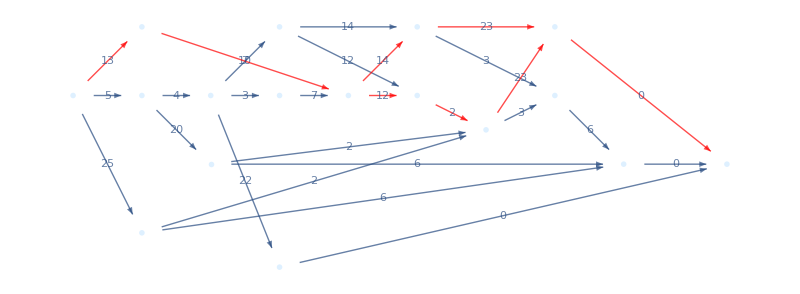

```mathematica
Graph[
edges,
VertexShape->vertexShapes,
VertexSize->0.6,
VertexLabelStyle->Bold,
VertexStyle->LightBlue,
VertexCoordinates->vertexCoords,
EdgeStyle->Flatten[Thread[#->Red]&/@critEdges],
EdgeLabels->edgeLabels,
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left},
ImageSize->800]
```

Математическая модель

```mathematica
e1=Table[Subscript[T, i]==Subscript[τ, i]+Subscript[t, i],{i,15}]
```

{T_1==t_1+τ_1,T_2==t_2+τ_2,T_3==t_3+τ_3,T_4==t_4+τ_4,T_5==t_5+τ_5,T_6==t_6+τ_6,T_7==t_7+τ_7,T_8==t_8+τ_8,T_9==t_9+τ_9,T_10==t_10+τ_10,T_11==t_11+τ_11,T_12==t_12+τ_12,T_13==t_13+τ_13,T_14==t_14+τ_14,T_15==t_15+τ_15}

```mathematica
i1=Table[Subscript[T, K]>=Subscript[T, i],{i,15}]
```

{T_K≥T_1,T_K≥T_2,T_K≥T_3,T_K≥T_4,T_K≥T_5,T_K≥T_6,T_K≥T_7,T_K≥T_8,T_K≥T_9,T_K≥T_10,T_K≥T_11,T_K≥T_12,T_K≥T_13,T_K≥T_14,T_K≥T_15}

```mathematica
i2=Subscript[τ,#⟦1⟧]>=Subscript[T,#⟦2⟧]&/@Flatten[Table[Thread[{i,dependA[i]}],{i,15}],1]
```

{τ_4≥T_2,τ_5≥T_2,τ_6≥T_5,τ_7≥T_5,τ_8≥T_5,τ_9≥T_1,τ_9≥T_6,τ_10≥T_9,τ_10≥T_7,τ_11≥T_9,τ_11≥T_7,τ_12≥T_3,τ_12≥T_4,τ_12≥T_11,τ_13≥T_10,τ_13≥T_12,τ_14≥T_10,τ_14≥T_12,τ_15≥T_3,τ_15≥T_4,τ_15≥T_13}

```mathematica
e2=Subscript[τ, #]==0&/@first
```

{τ_1==0,τ_2==0,τ_3==0}

```mathematica
Rule@@@Join[e1,e2]
```

{T_1→t_1+τ_1,T_2→t_2+τ_2,T_3→t_3+τ_3,T_4→t_4+τ_4,T_5→t_5+τ_5,T_6→t_6+τ_6,T_7→t_7+τ_7,T_8→t_8+τ_8,T_9→t_9+τ_9,T_10→t_10+τ_10,T_11→t_11+τ_11,T_12→t_12+τ_12,T_13→t_13+τ_13,T_14→t_14+τ_14,T_15→t_15+τ_15,τ_1→0,τ_2→0,τ_3→0}

```mathematica
ni1=i1/.Rule@@@e1/.Rule@@@e2
```

{T_K≥t_1,T_K≥t_2,T_K≥t_3,T_K≥t_4+τ_4,T_K≥t_5+τ_5,T_K≥t_6+τ_6,T_K≥t_7+τ_7,T_K≥t_8+τ_8,T_K≥t_9+τ_9,T_K≥t_10+τ_10,T_K≥t_11+τ_11,T_K≥t_12+τ_12,T_K≥t_13+τ_13,T_K≥t_14+τ_14,T_K≥t_15+τ_15}

```mathematica
ni2=i2/.Rule@@@e1/.Rule@@@e2
```

{τ_4≥t_2,τ_5≥t_2,τ_6≥t_5+τ_5,τ_7≥t_5+τ_5,τ_8≥t_5+τ_5,τ_9≥t_1,τ_9≥t_6+τ_6,τ_10≥t_9+τ_9,τ_10≥t_7+τ_7,τ_11≥t_9+τ_9,τ_11≥t_7+τ_7,τ_12≥t_3,τ_12≥t_4+τ_4,τ_12≥t_11+τ_11,τ_13≥t_10+τ_10,τ_13≥t_12+τ_12,τ_14≥t_10+τ_10,τ_14≥t_12+τ_12,τ_15≥t_3,τ_15≥t_4+τ_4,τ_15≥t_13+τ_13}

```mathematica
durRules=Table[Subscript[t, i]->durationA[i],{i,15}]
```

{t_1→13,t_2→5,t_3→25,t_4→20,t_5→4,t_6→3,t_7→10,t_8→22,t_9→7,t_10→14,t_11→12,t_12→2,t_13→3,t_14→23,t_15→6}

```mathematica
Minimize[Join[{Subscript[T, K]},ni1,ni2]/.durRules,Append[Table[Subscript[τ, i],{i,15}],Subscript[T, K]]]
```

{57,{τ_1→0,τ_2→0,τ_3→0,τ_4→12,τ_5→5,τ_6→9,τ_7→10,τ_8→9,τ_9→13,τ_10→20,τ_11→20,τ_12→32,τ_13→34,τ_14→34,τ_15→51,T_K→57}}